# Higgs to digluon via a stop loop - attempt 1 with the FeynArts pipeline

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`

<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

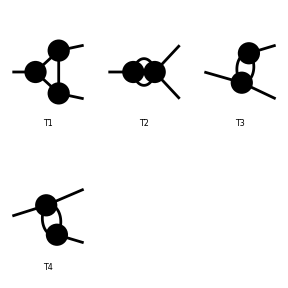

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSMQCD.mod

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 98 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 403 vertices

classes model {MSSMQCD} initialized

Excluding 0 Generic, 31 Classes, and 74 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 31 Classes, and 74 Particles fields

Restoring 18 field point(s)

in total: 3 Particles insertions

> Top. 1 ad/becf/dedfef.m, 2 diagrams

> Top. 2 ad/bece/dede.m, 1 diagram

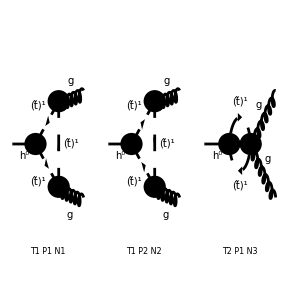

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[5],V[5]},InsertionLevel->{Particles},Model->"MSSMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[13,{2,3}],S[14],S[3],S[4],S[5],S[6],F[11],F[12],F[3],U[1],U[2],U[3],U[4]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[(*OffShell[*)CreateFeynAmp[diag1](*,2-> mg1,3-> mg2]*),FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{V[5,{Glu2}],k[2],0,{√3 ColorCharge}},{V[5,{Glu3}],k[3],0,{√3 ColorCharge}}}][-1/(12 CW MW π SB SW)Alfas EL Sub5 (Pair1 B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 (Pair1 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+Pair2 Pair3 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]))) Mat[SUN1]]

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[amp]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{V[5,{Glu2}],k[2],0,{√3 ColorCharge}},{V[5,{Glu3}],k[3],0,{√3 ColorCharge}}}][0]

0

#### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

mat= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-5.frm

running FORM...

ok

Note: polarization sum auto squares the matrix element. Subexpr seems to destroy this line.

```mathematica
(*mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify*)
```

# Input point

## Inputs

```mathematica
stopM1 = 170;
stopM2 = 1000;
mixT = 0;
muM = 250;
betaA = 1.47; (*tan beta = 10*)
alphaA = betaA - (Pi/2);
offM1 =0.0001;
offM2 = 0.0001;
Clear[matSq,c1,c2,ghSS,h11,h12,h22,z11,z12,z22,m,mh,mZ,mW]
```

# FeynArts Evaluation

## Numerical Evaluation

```mathematica
matPostSub = mat//.Subexpr[]//. mg1 -> offM1 //.mg2-> offM2
```

1/(9 CW2 MW2 π SB2 SW2)Alfa Alfas2 ((B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]-2 Mh02 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])) B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]^*+4 (-B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]+4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+2 Mh02 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])) C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+2 (-Mh02 (B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])+4 Mh02^2 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])) (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*)) (((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(-4 MW MZ SAB SB SW2 USf[1,2,3,3]+3 CW (MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+2 CA MT2 USf[1,2,3,3])) USfC[1,2,3,3]) (USf[1,1,3,3] ((6 CA CW MT2-MW MZ SAB SB (3-4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3])+USf[1,2,3,3] (-4 MW MZ SAB SB SW2 USfC[1,2,3,3]+3 CW (MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+2 CA MT2 USfC[1,2,3,3])))

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
Alfas->0.12,Alfas2->(0.12)^2,
SW2->0.2228,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,MUEC-> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),AfC[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat],USf[2,1,3,3]-> -Sin[thetat],USf[2,2,3,3]-> Cos[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=matPostSub//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

```mathematica
feynArtsResult =Chop[MyMatrixElement[stopM1,stopM2,mixT,muM,alphaA,betaA]]
```

0.172183

```mathematica
diphotonResults = 0.000123917 (*250,10000,0,250,-0.1008,1.47*)
```

0.000123917

```mathematica
diphotonResults*(Alfas/Alfa)^2*(2/9)*(9/4)^2 /. Alfas2-> (0.12)^2/.Alfa2-> (1/128)^2
```

0.0328901

```mathematica
%/feynArtsResult
```

0.191018

```mathematica
(*LogLogPlot[{MyMatrixElement[ms,10000,0,250,0,1.47]},{ms,200,1000}]*)
```

## Definitions and terminology

Notation for the diphoton decay:
p1= Momentum of 1st out-going particle (Z or photon)
p2= Momentum of 2nd out-going particle (photon)
mh= Mass of the decaying higgs
m = Mass of the stop
ghss= Higgs-stop coupling
α = Fine structure constant
x and y are Feynman parameters

Additional notation for the Zγ decay:
m1= Mass of the lighter stop mass eignestate
m2= Mass of the heavier stop mass eigenstate
zij= Coupling of the Z boson to stops of mass eigenstates ij = 11, 12, 21, 22
zgij= 4 point coupling of the Z boson and a photon to the stop mass eigenstates
hij= Higgs coupling to stops in their mass eigenstates (note: h11= ghSS)

After introducing all LO and NLO coefficients in this language, I will introduce the explicit dependence of these factors on MSSM parameters. See my summary Latex document for more details.

## Higgs to gg

Note: the (9/4)^2 is to ultimately cancel the electromagnetic change of 2/3 associated with the squarks and the (1/9) is to get rid of the three different colour diagrams built in for the diphoton case. The 2 is the proper colour factor of the diagram.

```mathematica
matSq =2*(1/9)*(9/4)^2*Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mg1,4],Times[Power[mg1,2],Plus[Times[4,Power[mg2,2]],Times[-2,Power[mh,2]]]],Power[Plus[Power[mg2,2],Times[-1,Power[mh,2]]],2]]],Times[6,c1,c2,Plus[Power[mg1,2],Power[mg2,2],Times[-1,Power[mh,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]](*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details. Adjustments for the differences between the diphoton and digluon case can be seen in front of the "Times[]" bracket.*)
```

(81 (c2^2 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2)+6 c1 c2 (mg1^2+mg2^2-mh^2) mZ^2+8 c1^2 mZ^4))/(16 v^2)

The c1 on-shell term is zero.

```mathematica
c2LOggInted = 2*(Rational[1, 18]*gs^2*ghSS*v*
     (mh^2 - 4*m1^2*ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]]^2))/(mh^4*Pi^2)
```

(ghSS gs^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2))/(9 mh^4 π^2)

## Coupling definitions

Explicitly, we can write out these couplings in terms of MSSM parameters - for more details see my summary Latex document.

#### Z couplings

```mathematica
z11=-(e/(2*sW*cW))*(ct^2 - 4sW^2/3)
```

-(e (ct^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z22=-(e/(2*sW*cW))*(st^2 - 4sW^2/3)
```

-(e (st^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z12=(e/(2*sW*cW))*(ct*st)
```

(ct e st)/(2 cW sW)

Within these expressions, e is the elementary charge, s_W and c_W are the sine and cosine of the Weinberg angle, and c_t is the cosine of the stop mixing angle.

#### Z-γ couplings

```mathematica
zg11=(2e^2/(3*sW*cW))*(ct^2 - 4sW^2/3)
```

(2 e^2 (ct^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg22=(2e^2/(3*sW*cW))*(st^2 - 4sW^2/3)
```

(2 e^2 (st^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg12=-(2e^2/(3*sW*cW))*(ct*st)
```

-(2 ct e^2 st)/(3 cW sW)

#### Higgs couplings

```mathematica
h11= a*ct^2 +b*st^2 +2*c*ct*st
```

a ct^2+2 c ct st+b st^2

```mathematica
h22 = a*st^2 +b*ct^2 -2*c*ct*st
```

b ct^2-2 c ct st+a st^2

```mathematica
h12= -a*ct*st +b*ct*st +c*(ct^2-st^2)
```

-a ct st+b ct st+c (ct^2-st^2)

Where we have (in the decoupling limit)

```mathematica
a=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](1/2 -2*sW^2/3)
```

-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW)

```mathematica
b=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](2*sW^2/3)
```

-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW)

```mathematica
c = ((e*mt)/(2*mW*sW))(At-μ*Cot[β])
```

(e mt (At-μ Cot[β]))/(2 mW sW)

μ and β  are your standard MSSM paramters, m_t is the mass of the top, and A_t is a soft breaking term that can be expressed in terms of the stop mixing parameter and μ.

```mathematica
SUBIN[stopMass1_,stopMass2_,xt_,mu_,beta_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
Alfa->1/128,Alfa2->(1/128)^2,
Alfas->0.12,Alfas2-> (0.12^2),
sW->0.4796,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],gs-> Sqrt[(4*Pi*Alfas)],
m1->stopMass1,m2->stopMass2,
At-> ((xt)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[stopMass1_,stopMass2_,xt_,mu_,beta_]:=matToSub//.SUBIN[stopMass1,stopMass2,xt,mu,beta]//Simplify
```

## Plug in values and compare to FeynArts result

```mathematica
c1 = 0//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2
```

0

```mathematica
c2 =c2LOggInted //. ghSS-> h11//.M1->mg1^2//.M2->mg2^2
```

(gs^2 v (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)

```mathematica
matSq
```

1/(16 mh^8 π^4)gs^4 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2) (mh^2-4 m1^2 ArcTan[mh/(√(4 m1^2-mh^2))]^2)^2 (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW))^2

## Results

```mathematica
myCalcResult = matSq//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

6.85118×10^-10 (mg1^4+(-15625+mg2^2)^2+mg1^2 (-31250+4 mg2^2))

```mathematica
myCalcResultNum = Chop[myCalcResult/. mg1->offM1/.mg2->offM2]
```

0.167265

```mathematica
loResult =myCalcResultNum/feynArtsResult
```

0.971436

## Check numerical result of the full expressions for c1 and c2

```mathematica
c1 = Times[Rational[1,18],ghSS,Power[gs,2],Power[mZ,-2],Power[Pi,-2],v,Power[Plus[Power[m1,2],Times[M1,Plus[-1,x],x],Times[-1,M2,y],Times[-1,Plus[Times[-1,M1],Times[-1,M2],Power[mh,2]],x,y],Times[M2,Power[y,2]]],-1],Power[Plus[Power[m1,2],Times[-1,Power[mh,2],x,y],Times[M1,x,Plus[-1,x,y]],Times[M2,y,Plus[-1,x,y]]],-1],Plus[Times[-1,Power[M1,2],Power[x,2],Plus[-1,Times[2,x]],Plus[-1,x,y]],Times[M1,x,Plus[Times[2,Plus[Times[-1,M1],Times[-1,M2],Power[mh,2]],x,Power[y,2]],Times[-2,M2,y,Power[Plus[-1,x,y],2]],Times[Plus[-1,Times[2,x]],Plus[Times[-1,Power[m1,2]],Times[Power[mh,2],x,y]]]]],Times[y,Plus[Times[2,Plus[M2,Times[-1,Power[mh,2]]],Plus[Times[-1,M1],Times[-1,M2],Power[mh,2]],Power[x,2],y],Times[2,Power[Plus[Times[-1,M1],Times[-1,M2],Power[mh,2]],2],Power[x,2],y],Times[-1,M2,Plus[-1,Times[2,y]],Plus[Power[m1,2],Times[-1,Power[mh,2],x,y],Times[M2,y,Plus[-1,x,y]]]]]]]]
```

(ghSS gs^2 v (-M1^2 x^2 (-1+2 x) (-1+x+y)+M1 x (2 (-M1-M2+mh^2) x y^2-2 M2 y (-1+x+y)^2+(-1+2 x) (-m1^2+mh^2 x y))+y (2 (M2-mh^2) (-M1-M2+mh^2) x^2 y+2 (-M1-M2+mh^2)^2 x^2 y-M2 (-1+2 y) (m1^2-mh^2 x y+M2 y (-1+x+y)))))/(18 mZ^2 π^2 (m1^2+M1 (-1+x) x-M2 y-(-M1-M2+mh^2) x y+M2 y^2) (m1^2-mh^2 x y+M1 x (-1+x+y)+M2 y (-1+x+y)))

```mathematica
c1 = c1/(v)//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2 (*Divide these out so we can numerically integrate*)
```

(gs^2 (-mg1^4 x^2 (-1+2 x) (-1+x+y)+mg1^2 x (2 (-mg1^2-mg2^2+mh^2) x y^2-2 mg2^2 y (-1+x+y)^2+(-1+2 x) (-m1^2+mh^2 x y))+y (2 (mg2^2-mh^2) (-mg1^2-mg2^2+mh^2) x^2 y+2 (-mg1^2-mg2^2+mh^2)^2 x^2 y-mg2^2 (-1+2 y) (m1^2-mh^2 x y+mg2^2 y (-1+x+y)))) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(18 mZ^2 π^2 (m1^2+mg1^2 (-1+x) x-mg2^2 y-(-mg1^2-mg2^2+mh^2) x y+mg2^2 y^2) (m1^2-mh^2 x y+mg1^2 x (-1+x+y)+mg2^2 y (-1+x+y)))

```mathematica
c2 =Times[Rational[-2,9],ghSS,Power[gs,2],Power[Pi,-2],v,x,y,Power[Plus[Power[m1,2],Times[-1,M1,x],Times[M1,Power[x,2]],Times[-1,M2,y],Times[-1,Plus[Times[-1,M1],Times[-1,M2],Power[mh,2]],x,y],Times[M2,Power[y,2]]],-1]]
```

-(2 ghSS gs^2 v x y)/(9 π^2 (m1^2-M1 x+M1 x^2-M2 y-(-M1-M2+mh^2) x y+M2 y^2))

```mathematica
c2 =c2/(v)//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2(*Divide these out so we can numerically integrate*)
```

-(2 gs^2 x y (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 π^2 (m1^2-mg1^2 x+mg1^2 x^2-mg2^2 y-(-mg1^2-mg2^2+mh^2) x y+mg2^2 y^2))

```mathematica
c1 = c1//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

(mg1^2 (-0.000224765+0.00044953 x) x+mg2^2 (-0.000224765+0.00044953 y) y)/(28900.-15625. x y+mg1^2 x (-1.+x+y)+mg2^2 y (-1.+x+y))

```mathematica
c1 = c1 //. mg1-> offM1 //.mg2 -> offM2
```

(1.×10^-8 (-0.000224765+0.00044953 x) x+1.×10^-8 (-0.000224765+0.00044953 y) y)/(28900.-15625. x y+1.×10^-8 x (-1.+x+y)+1.×10^-8 y (-1.+x+y))

```mathematica
c1 =-3.3*10^-32(*NIntegrate[c1,{x,0,1},{y,0,(1-x)}] Really slow so I'm removing it*)
```

-3.3×10^-32

```mathematica
c2 = c2//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

(7.47788 x y)/(28900.-15625. x y+mg1^2 x (-1.+x+y)+mg2^2 y (-1.+x+y))

```mathematica
c2 = c2//. mg1-> offM1 //.mg2 -> offM2
```

(7.47788 x y)/(28900.-15625. x y+1.×10^-8 x (-1.+x+y)+1.×10^-8 y (-1.+x+y))

```mathematica
c2 =NIntegrate[c2,{x,0,1},{y,0,(1-x)}]
```

0.0000116332

```mathematica
testMatSq = matSq*(v)^2/.ghSS-> h11//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

0.167265+6.85118×10^-10 mg1^4-0.0000214099 mg2^2+6.85118×10^-10 mg2^4+mg1^2 (-0.0000214099+2.74047×10^-9 mg2^2)

```mathematica
testMatSq = testMatSq/. mg1-> offM1 //.mg2 -> offM2
```

0.167265

```mathematica
fullResult =testMatSq/feynArtsResult
```

0.971436

# Result

```mathematica
loResult
fullResult
```

0.971436

0.971436